## recursive algorithm

```mathematica
pard=Import[FileNameJoin[{NotebookDirectory[],"parameters_sizetunings_direct.csv"}]];
(*PARAMETERS FROM GAUSSIAN/ERFS FITS OF EXPERIMENTAL RATE FIELDS*)
tabd=pard[[;;,4;;7]];
bd=Join[pard[[;;,1]],{0}];
kdc=pard[[;;,2]];(*THESE ARE IN DEGREES*)
kd=pard[[;;,3]];
rdA[s_]=Join[Table[tabd[[b,1]]Erf[s/tabd[[b,3]]]-tabd[[b,2]]Erf[s/tabd[[b,4]]],{b,1,6}],{Sqrt[s]}];
σ[s_]:=Join[Table[kd[[b]] s+kdc[[b]],{b,1,6}],{20}];
Subscript[σ, AB]={{7,5,4,0,7,15,0},{5,6,6,0,7,15,0},{8,6,0,6,0,15,15},{5,6,6,0,0,15,0}};
Subscript[σ2, ABp][s_]:=Table[(Subscript[σ, AB][[a,b]])^2+(σ[s][[b]])^2,{a,1,4},{b,1,7}];
smindir=5;
smaxdir=85;
Ntrials=5;
Ncycles=2;
Nthreads=100;
bestA=ConstantArray[0,{4,7,Nthreads}];
scoresA=ConstantArray[0,{4,7,Nthreads}];
TA=ConstantArray[0,{4}];
```

```mathematica
(*SLOW*)
(*aa indicates the celltype of the self consistency equations i am considering, i.e. only 4 cell types in L2/3*)
For[nt=1,nt≤Nthreads,nt++,{count=1;rdA[s_]=Join[Table[tabd[[b,1]]Erf[s/tabd[[b,3]]]-tabd[[b,2]]Erf[s/tabd[[b,4]]],{b,1,6}],{Sqrt[s]}];For[aa=1,aa≤4,aa++,{
qA[s]:=Sqrt[rdA[s]+bd]-Sqrt[bd];
Subscript[v, 1]=NIntegrate[(qA[s][[aa]])^2(σ[s][[aa]])^2,{s,smindir,smaxdir}];
Subscript[v, 2]= 2Table[NIntegrate[qA[s][[aa]]rdA[s][[b]] 2(σ[s][[aa]])^2 (σ[s][[b]])^2/(2(σ[s][[aa]])^2+Subscript[σ2, ABp][s][[aa,b]]),{s,smindir,smaxdir}],{b,1,7}];
Subscript[v, 3]= Table[NIntegrate[rdA[s][[b]]rdA[s][[c]](σ[s][[b]])^2(σ[s][[c]])^2/ (Subscript[σ2, ABp][s][[aa,b]]+Subscript[σ2, ABp][s][[aa,c]]),{s,smindir,smaxdir}],{c,1,7},{b,1,7}];
(*ERROR FUNCTION*)
Subscript[S, A][ws_]:=Subscript[v, 1]-Sum[ws[[b]] Subscript[v, 2][[b]],{b,1,7}]+Sum[Sum[ws[[b]]ws[[c]]Subscript[v, 3][[b,c]],{c,1,7}],{b,1,7}];
WAs={WAE,WAP,WAS,WAV,WA4,WAM,WAMe};
Subscript[μ, AB]=2Table[NIntegrate[qA[s][[aa]]rdA[s][[b]] (σ[s][[aa]])^2 (σ[s][[b]])^2/(2(σ[s][[aa]])^2+Subscript[σ2, ABp][s][[aa,b]]),{s,smindir,smaxdir}],{b,1,7}];
Subscript[ν, ABC]=Table[NIntegrate[rdA[s][[b]]rdA[s][[c]](σ[s][[b]])^2(σ[s][[c]])^2/ (Subscript[σ2, ABp][s][[aa,b]]+Subscript[σ2, ABp][s][[aa,c]]),{s,smindir,smaxdir}],{c,1,7},{b,1,7}];
Clear[WAE,WAP,WAS,WAV,WA4,WAM,WAMe];
start:={{RandomReal[],-RandomReal[],-RandomReal[],0.,RandomReal[],RandomReal[],0.},{RandomReal[],-RandomReal[],-RandomReal[],0.,RandomReal[],RandomReal[],0.},{RandomReal[],-RandomReal[],0.,-RandomReal[],0.,RandomReal[],RandomReal[]},{RandomReal[],-RandomReal[],-RandomReal[],0.,0.,RandomReal[],0.}};
conditions={{WAE>0,WAP<0,WAS<0,WAV->0,WA4>0,WAM>0,WAMe->0},{WAE>0,WAP<0,WAS<0,WAV->0,WA4>0,WAM>0,WAMe->0},{WAE>0,WAP<0,WAS->0,WAV<0,WA4->0,WAM>0,WAMe>0},{WAE>0,WAP<0,WAS<0,WAV->0,WA4->0,WAM>0,WAMe->0}};
startpoint[p1_,p2_,p3_,p4_,p5_,p6_]:={WAs[[p1]]->stpts[[p1]],WAs[[p2]]->stpts[[p2]],WAs[[p3]]->stpts[[p3]],WAs[[p4]]->stpts[[p4]],WAs[[p5]]->stpts[[p5]],WAs[[p6]]->stpts[[p6]]};
cond=conditions[[aa]];
(*solve for population v6,keeping the other values constrained, i1 is the index of the equation that i try to solve*)
sol[{p1_,p2_,p3_,p4_,p5_,p6_},v6_,i1_]:=Quiet[Reduce[{Subscript[μ, AB][[i1]]-Sum[Subscript[ν, ABC][[b,i1]]WAs[[b]],{b,1,7}]==0,cond[[v6]]}/.startpoint[p1,p2,p3,p4,p5,p6],WAs[[v6]]]];
Print["Elapsed time is:"];
Timing[
bestmods={};
scores={};
(*start from Ntrials random initial conditions*)
For[icond=1,icond≤ Ntrials,icond++,
stpts=start[[aa]];
bestmod=stpts;
isbetter=Subscript[S, A][stpts];
(*Print["stpts starts at ",stpts," with Sk ",Sk[stpts]];*)
(*try to improve bestmod for several attempts*)
For[attempt=1,attempt<3,attempt++,
{vs=RandomSample[Permutations[Range[1,7]],1];
For[pop=1,pop≤7,pop++,
{v6=vs[[1,pop]];
val={};
valSk={};
stptstemp=stpts;
For[i1=1,i1≤7,i1++,
{(*Print["solving eq ",i1," for variable " v6];*)
sn=sol[Complement[Range[1,7],{v6}],v6,i1];
(*length(s)>1 if Reduce found a solution that satisfies constraints*)
If[Length[sn]>1,{val=Append[val,sn[[2]]];stptstemp[[v6]]=sn[[2]];valSk=Append[valSk,Subscript[S, A][stptstemp]];}]}];
(*if it improves Sk keep the new value of pop v6 as starting point*)
If[Length[valSk]>0,{eqbest=Position[valSk,Min[valSk]][[1,1]];
stptstemp[[v6]]=val[[eqbest]];If[Subscript[S, A][stptstemp]<isbetter,{isbetter=Subscript[S, A][stptstemp],stpts=stptstemp}]}]}]}];(*Print["stops at ",stpts," with Sk ",Sk[stpts]];*)
bestmods=Append[bestmods,stpts];
scores=Append[scores,Subscript[S, A][stpts]];];
(*kbest=Position[scores,Min[scores]][[1,1]];
Print[bestmods[[kbest]],"with best score ",scores[[kbest]]];*)
sortedscores=Sort[scores];][[1]];
bestmod1=bestmods[[Position[scores,sortedscores[[1]]][[1,1]]]];
TA[[aa]]=Sqrt[bd[[aa]]]-Sum[bestmod1[[c]]bd[[c]],{c,1,6}];
newrdA[s_]=(Sum[bestmod1[[i]]((σ[s][[i]])^2/(Subscript[σ2, ABp][s][[aa,i]]) rdA[s][[i]]+bd[[i]]),{i,1,7}]+TA[[aa]])^2-bd[[aa]];
rdA[s_]=Join[rdA[s][[;;aa-1]],{newrdA[s]},rdA[s][[aa+1;;]]];
Print[aa];
(*Print["3 best mods are: "];
Table[Print[bestmods[[Position[scores,sortedscores[[i]]][[1,1]]]]," with score ",sortedscores[[i]]],{i,1,3}];*)bestA[[aa,;;,nt]]=bestmod1;scoresA[[aa,;;,nt]]=scores[[1]];
If[count<Ncycles,
If[aa==4,{aa=0;count++}]]}];Export[StringJoin["/Users/serena/Dropbox/inferredWAB_recurrentseries",ToString[nt],".csv"],Abs[bestA[[;;,;;,nt]]]];
Export[StringJoin["/Users/serena/Dropbox/inferredTA_recurrentseries",ToString[nt],".csv"],TA];}]
```

## Model (parameters set) comparison

```mathematica
ctnsF={"AllFR_Pyr","AllFR_PV","AllFR_SOM","AllFR_VIP","FFInputL4","FFinputLM"};
sizs=Table[s,{s,5,85,10}];
Nn=30;
center=Round[Nn/2];
fr0=Import["/Users/serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/SSNdoc/the_path_to_the_hole/Data/InverseData2/FR0d_fromoccupancy.csv"];(*this is 6*10*)
datfrpref=Table[Max[fr0[[ct,;;]]],{ct,1,6}];
(*this position includes size=0*)
parentdir="/Users//serenadisanto/Dropbox/AllProjects/ColumbiaProjects/Massimo-Andi-Morgane/SSN/SSN4ct_after_leastsquares_analyt+bias/newOctober_forpaper+supp/modelrecursive";
FieldDirExists[thread_,s_,ct_]:=FileExistsQ[StringJoin[parentdir,ToString[thread],"/",ctnsF[[ct]],"_Dirsiz",ToString[sizs[[s]]],"_",ToString[thread],".txt"]];
LoadFieldCentDir[thread_,s_,ct_]:=Import[StringJoin[parentdir,ToString[thread],"/",ctnsF[[ct]],"_Dirsiz",ToString[sizs[[s]]],"_",ToString[thread],".txt"],"Data"][[center,center]];
LoadFieldCentInv[thread_,s_,ct_]:=Import[StringJoin[parentdir,ToString[thread],"/",ctnsF[[ct]],"_Invsiz",ToString[sizs[[s]]],"_",ToString[thread],".txt"],"Data"][[center,center]];
RealQ[x_]:=Element[x,Reals]===True;
```

```mathematica
(*Elapsed time will be around 1.2*Nmods seconds, i.e. around 2 mins*)
Nmods=100;
Errorf1=ConstantArray[0,Nmods];
Errorf2=ConstantArray[0,Nmods];
Timing[For[mod=1,mod≤Nmods,mod++,{
fieldcents=Table[Quiet[LoadFieldCentDir[mod,ss,ct]],{ss,1,Length[sizs]},{ct,1,4}];
st=Table[If[RealQ[fieldcents[[ss,ct]]]&&FieldDirExists[mod,ss,ct]&&fieldcents[[ss,ct]]<10^4&&fieldcents[[ss,ct]]>10^-4,fieldcents[[ss,ct]],10^3],{ss,1,Length[sizs]},{ct,1,4}];
frpref=Table[If[Max[st[[;;,ct]]]<10^3,Max[st[[;;,ct]]],10^-4],{ct,1,4}];
Errorf1[[mod]]=Sum[(fr0[[ct,ss+1]]-st[[ss,ct]])^2,{ss,1,Length[sizs]},{ct,1,4}];Errorf2[[mod]]=Sum[(fr0[[ct,ss+1]]/datfrpref[[ct]]-st[[ss,ct]]/frpref[[ct]])^2,{ss,1,Length[sizs]},{ct,1,4}];}]];
```

```mathematica
For[mod=1,mod≤100,mod++,{If[Errorf1[[mod]]≥300,Errorf1[[mod]]=375];If[Errorf2[[mod]]≥8,Errorf2[[mod]]=8.5]}];
```

```mathematica
optionsf1:={Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["normalized error",30,Darker[Gray]],None},{Style["absolute error",30,Darker[Gray]],None}},FrameTicks->{{{0,3,6},None},{{0,50,150,250},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
```

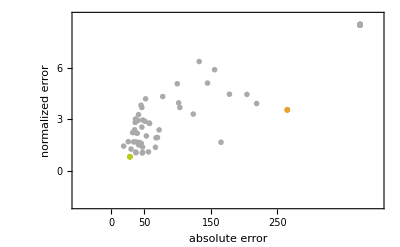

```mathematica
{b1,h1}=HistogramList[Errorf1,10];
{b2,h2}=HistogramList[Errorf2,7];
bestmod=37;
worstmod=33;
modcomp=Show[ListPlot[Table[{Errorf1[[mod]],Errorf2[[mod]]},{mod,1,Nmods}],PlotMarkers->{●,17},PlotStyle->Lighter[Gray],PlotRange->{{-50,402},{-2,9}},Evaluate[optionsf1]],ListPlot[{{Errorf1[[bestmod]],Errorf2[[bestmod]]}},PlotMarkers->{●,12},PlotStyle->ColorData[10]/@{5}],ListPlot[{{Errorf1[[worstmod]],Errorf2[[worstmod]]}},PlotMarkers->{●,12},PlotStyle->ColorData[10]/@{3}]]
```

## Best & worst model

```mathematica
thismod=37;
parentdir1="/Users/serenadisanto/Dropbox/";
(*make this nicer by implementing ./*)
W1=Import[StringJoin[parentdir1,"inferredWAB_recurrentseries",ToString[thismod],".csv"]];
T1=Import[StringJoin[parentdir1,"inferredTA_recurrentseries",ToString[thismod],".csv"]];
W1[[;;,2;;4]]=-W1[[;;,2;;4]];
WM=Table[Flatten[Join[W1[[i,1;;6]],T1[[i]]]],{i,1,4}];
mp=MatrixPlot[WM[[;;,1;;7]],FrameTicks->{{{{1,"Pyr"},{2,"PV"},{3,"SOM"},{4,"VIP"}},None},{None,{{1,"Pyr"},{2,"PV"},{3,"SOM"},{4,"VIP"},{5,"L4"},{6,"LM"},{7,"bias"}}}},FrameTicksStyle->Directive[20,Darker[Gray]],PlotLegends->True]
```

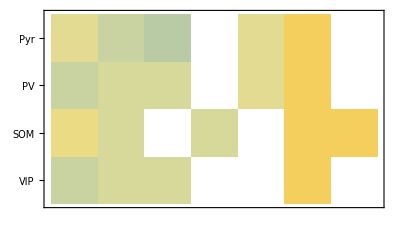

```mathematica
ms=MatrixPlot[Subscript[σ, AB],ColorFunction->"StarryNightColors",ColorRules->{0->White},FrameTicks->{{{{1,"Pyr"},{2,"PV"},{3,"SOM"},{4,"VIP"}},None},{None,{{1,"Pyr"},{2,"PV"},{3,"SOM"},{4,"VIP"},{5,"L4"},{6,"LM"}}}},FrameTicksStyle->Directive[22,Darker[Gray]]]
```

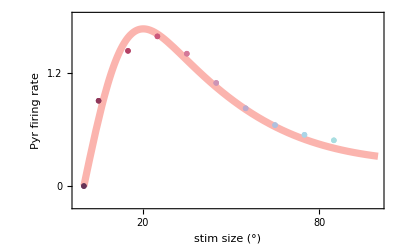

```mathematica
colorgrads={"CandyColors","LightTerrain","AvocadoColors","PearlColors","BeachColors","CoffeeTones","RedBlueTones"};
colors={RGBColor[251/255,180/255,174/255],RGBColor[179/255,205/255,227/255],RGBColor[204/255,235/255,197/255],RGBColor[222/255,203/255,228/255],RGBColor[254/255,217/255,166/255],RGBColor[229/255,216/255,189/255],RGBColor[229/255,181/255,201/255]};
(*ranges for 37*)
pltrang1d={{-.2,1.8},{-0.5,5.6},{-0.2,2.8},{-0.1,1}};
tickf1d={{0,1.2},{0,4},{0.,2.5},{0,0.8}};
(*ranges for 82*)
(*pltrang1d={{-.2,1.2},{-0.5,5.6},{-0.2,2.8},{-0.05,0.4},{-0.15,.9},{-0.05,1.1},{-0.7,1.7}};
tickf1d={{0,0.8},{0,4},{0.,2.},{0,0.2},{0,0.8},{0,0.8},{0,1}};*)
optionsf1:={PlotRange->{{-2,100},pltrang1d[[aa]]},PlotStyle->{Thickness[0.013],colors[[aa]]},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["Pyr firing rate",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{tickf1d[[aa]],None},{{20,80},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
sizs0=Join[{0},Table[s,{s,5,85,10}]];
sizs=Table[s,{s,5,85,10}];
LoadFieldDir[thread_,s_,ct_]:=Import[StringJoin[parentdir,ToString[thread],"/",ctnsF[[ct]],"_Dirsiz",ToString[sizs[[s]]],"_",ToString[thread],".txt"],"Data"];
LoadFieldInv[thread_,s_,ct_]:=Import[StringJoin[parentdir,ToString[thread],"/",ctnsF[[ct]],"_Invsiz",ToString[sizs[[s]]],"_",ToString[thread],".txt"],"Data"];
(*parameters for 37*)
parfitsd={{2.7,0.91,16,65},{11,0.96,18,50},{2.35,0,16,90},{0.9,0.74,2,20}};
Subscript[rd, fits][s_]:=Table[parfitsd[[b,1]](Erf[s/parfitsd[[b,3]]]-parfitsd[[b,2]]Erf[s/parfitsd[[b,4]]]),{b,1,4}];
aa=1;
st1=Join[{0},Table[LoadFieldCentDir[thismod,s,aa],{s,1,Length[sizs]}]];
f1=Show[{Plot[Subscript[rd, fits][s][[aa]],{s,0,100},Evaluate[optionsf1]],ListPlot[Table[{{sizs0[[i]],st1[[i]]}},{i,1,Length[sizs0]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]]}]
```

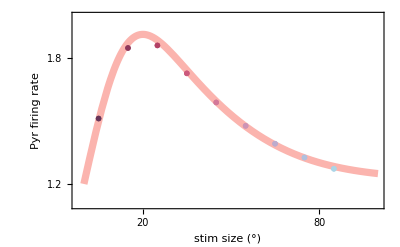

```mathematica
thismod=37;
optionsf1i:={PlotRange->{{-2,100},pltrang1i[[aa]]},PlotStyle->{Thickness[0.013],colors[[aa]]},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["Pyr firing rate",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{tickf1i[[aa]],None},{{20,80},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
pltrang1i={{1.1,2.},{2.9,6.1},{1,2.4},{0.35,.6}};
tickf1i={{1.2,1.8},{4,6},{1.2,2.},{0.4,0.6}};
parfitsi={{1.3,0.98,17,60,1.2},{4.8,0.95,16,60,3.},{1.65,0.004},{0.2,1.5,4,18,0.25,80,0.41}};
Subscript[ri, fits][s_]:=Join[Table[parfitsi[[b,1]](Erf[s/parfitsi[[b,3]]]-parfitsi[[b,2]]Erf[s/parfitsi[[b,4]]])+parfitsi[[b,5]],{b,1,2}],{parfitsi[[3,1]]-parfitsi[[3,2]]s},{parfitsi[[4,1]](Erf[s/parfitsi[[4,3]]]-parfitsi[[4,2]]Erf[s/parfitsi[[4,4]]])+parfitsi[[4,5]]Erf[s/parfitsi[[4,6]]]+parfitsi[[4,7]]}];
aa=1;
st1=Table[LoadFieldCentInv[thismod,s,aa],{s,1,Length[sizs]}];
f1=Show[{Plot[Subscript[ri, fits][s][[aa]],{s,0,100},Evaluate[optionsf1i]],ListPlot[Table[{{sizs[[i]],st1[[i]]}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]]}]
```

## PV paradoxical

remember! to simulate you need to copy the parameters sets in WAB and TA in a new file named with the thread that you want, in this case 1001

```mathematica
LoadFieldEvolveDir[thread_,s_]:=Import[StringJoin[parentdir,ToString[thread],"/FR_ts_Dirsiz",ToString[sizs[[s]]],"_",ToString[thread],".txt"],"Data"];
thismod=37;
noPVmod=1001;
evolvectrl=LoadFieldEvolveDir[thismod,3];
evolvenoPV=LoadFieldEvolveDir[noPVmod,3];
```

```mathematica
optionsf2={PlotRange->All,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["firing rate",30,Darker[Gray]],None},{Style["time",30,Darker[Gray]],None}},FrameTicksStyle->Directive[30,Darker[Gray]],Method->"DefaultPlotStyle"->Thickness[0.02],PlotStyle->{colors[[1]],colors[[2]],colors[[3]],colors[[4]]},Joined->True};
```

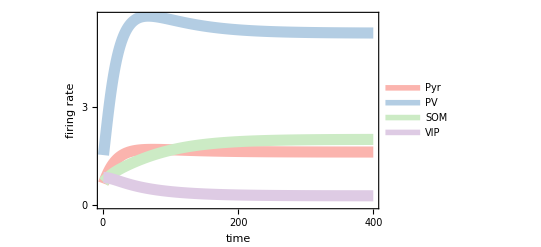

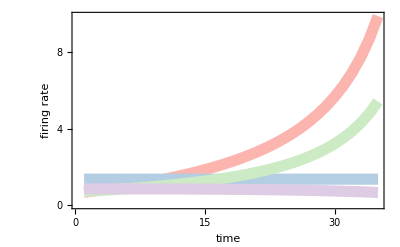

```mathematica
f1=ListPlot[Transpose[evolvectrl[[1;;400,;;]]],FrameTicks->{{{0,3,6},None},{{0,200,400},None}},Evaluate[optionsf2],PlotLegends->{Style["Pyr",25,Darker[Gray]],Style["PV",25,Darker[Gray]],Style["SOM",25,Darker[Gray]],Style["VIP",25,Darker[Gray]]}]
f2=ListPlot[Transpose[evolvenoPV[[1;;35,;;]]],Evaluate[optionsf2],FrameTicks->{{{0,4,8},None},{{0,15,30},None}}]
```

## HVA silencing

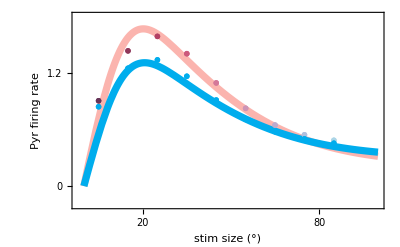

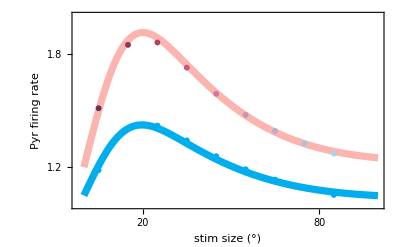

```mathematica
aa=1;
thismod=37;
HVAsilencemod=1002;
colorlaser=RGBColor[0,173/255,237/255];
stctrl=Table[LoadFieldCentDir[thismod,s,aa],{s,1,Length[sizs]}];
stHVAsilencemod=Table[LoadFieldCentDir[HVAsilencemod,s,aa],{s,1,Length[sizs]}];
Subscript[rdsil, fit][s_]:=parfitsdsil[[1]](Erf[s/parfitsdsil[[3]]]-parfitsdsil[[2]]Erf[s/parfitsdsil[[4]]]);
Subscript[risil, fit][s_]:=parfitsisil[[1]](Erf[s/parfitsisil[[3]]]-parfitsisil[[2]]Erf[s/parfitsisil[[4]]])+parfitsisil[[5]];
parfitsdsil={2.05,0.85,16,65};
parfitsisil={0.7,1.02,17,60,1.05};
pltrang1i={{1.,2.},{2.9,6.1},{1,2.4},{0.35,.6}};
f1=Show[{Plot[Subscript[rd, fits][s][[aa]],{s,0,100},Evaluate[optionsf1]],Plot[Subscript[rdsil, fit][s],{s,0,100},PlotStyle->{Thickness[0.013],colorlaser},Evaluate[optionsf1]],ListPlot[Table[{{sizs[[i]],stctrl[[i]]}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]],ListPlot[Table[{{sizs[[i]],stHVAsilencemod[[i]]}},{i,1,Length[sizs]}],PlotStyle->colorlaser,PlotMarkers->{●,20},Evaluate[optionsf1]]}]
stctrli=Table[LoadFieldCentInv[thismod,s,aa],{s,1,Length[sizs]}];
stHVAsilencemodi=Table[LoadFieldCentInv[HVAsilencemod,s,aa],{s,1,Length[sizs]}];
f2=Show[{Plot[Subscript[ri, fits][s][[aa]],{s,0,100},Evaluate[optionsf1i]],Plot[Subscript[risil, fit][s],{s,0,100},PlotStyle->{Thickness[0.013],colorlaser},Evaluate[optionsf1i]],ListPlot[Table[{{sizs[[i]],stctrli[[i]]}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]],ListPlot[Table[{{sizs[[i]],stHVAsilencemodi[[i]]}},{i,1,Length[sizs]}],PlotStyle->colorlaser,PlotMarkers->{●,20},Evaluate[optionsf1]]}]
```

## SOM hyperpolarized

```mathematica
optionsf1mod:={PlotRange->All,PlotStyle->{Thickness[0.013],colors[[aa]]},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,FrameLabel->{{Style["normalized 
Pyr firing rate",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{tickf1d[[aa]],None},{{20,80},None}},FrameTicksStyle->Directive[30,Darker[Gray]]};
```

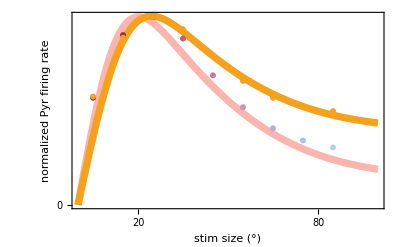

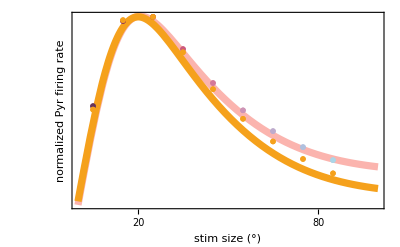

```mathematica
aa=1;
SOMhyperpolmod=1003;
colorSOMhyperpol=RGBColor[245/255,161/255,28/255];
stSOMhyperpolmod=Table[LoadFieldCentDir[SOMhyperpolmod,s,aa],{s,1,Length[sizs]}];
Subscript[rdhyp, fit][s_]:=parfitsdhyp[[1]](Erf[s/parfitsdhyp[[3]]]-parfitsdhyp[[2]]Erf[s/parfitsdhyp[[4]]]);
Subscript[rihyp, fit][s_]:=parfitsihyp[[1]](Erf[s/parfitsihyp[[3]]]-parfitsihyp[[2]]Erf[s/parfitsihyp[[4]]])+parfitsihyp[[5]];
parfitsdhyp={1.6,0.75,19,65};
parfitsihyp={0.66,0.9,17,60,0.62};
md=MaxValue[Subscript[rd, fits][q][[aa]],q];
mdl=Max[stctrl];
mdly=Max[stSOMhyperpolmod];
f1=Show[{Plot[Subscript[rd, fits][s][[aa]]/md,{s,0,100},Evaluate[optionsf1mod]],Plot[Subscript[rdhyp, fit][s],{s,0,100},PlotStyle->{Thickness[0.013],colorSOMhyperpol},Evaluate[optionsf1mod]],ListPlot[Table[{{sizs[[i]],stctrl[[i]]/mdl}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1mod]],ListPlot[Table[{{sizs[[i]],stSOMhyperpolmod[[i]]/mdly}},{i,1,Length[sizs]}],PlotStyle->colorSOMhyperpol,PlotMarkers->{●,20},Evaluate[optionsf1mod]]}]
stSOMhyperpolmodi=Table[LoadFieldCentInv[SOMhyperpolmod,s,aa],{s,1,Length[sizs]}];
mdi=MaxValue[Subscript[ri, fits][q][[aa]],q];
mdli=Max[stctrli];
mdliy=Max[stSOMhyperpolmodi];
f3=Show[{Plot[Subscript[rihyp, fit][s],{s,0,100},Evaluate[optionsf1mod]],Plot[Subscript[ri, fits][s][[aa]]/mdi,{s,0,100},PlotStyle->{Thickness[0.013],colorSOMhyperpol},Evaluate[optionsf1mod]],ListPlot[Table[{{sizs[[i]],stSOMhyperpolmodi[[i]]/mdliy}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1mod]],ListPlot[Table[{{sizs[[i]],stctrli[[i]]/mdli}},{i,1,Length[sizs]}],PlotStyle->colorSOMhyperpol,PlotMarkers->{●,20},Evaluate[optionsf1]]}]
```

## Contrast

```mathematica
aa=1;
thismod=37;
colorcontrast=ColorData[10]/@{2,3,4};
stctrl=Table[LoadFieldCentDir[thismod,s,aa],{s,1,Length[sizs]}];
stcontrasts=Table[LoadFieldCentDir[c,s,aa],{s,1,Length[sizs]},{c,1004,1005}];
Subscript[rdcs, fit][s_]:=Table[parfitsdcs[[c,1]](Erf[s/parfitsdcs[[c,3]]]-parfitsdcs[[c,2]]Erf[s/parfitsdcs[[c,4]]]),{c,1,2}];
Subscript[rics, fit][s_]:=Table[parfitsics[[c,1]](Erf[s/parfitsics[[c,3]]]-parfitsics[[c,2]]Erf[s/parfitsics[[c,4]]])+parfitsics[[c,5]],{c,1,2}];
parfitsdcs={{2.05,0.85,16,65},{1.65,0.8,16,65}};
parfitsics={{1.1,.98,17,60,1.05},{0.6,1.02,17,60,.9}};
pltrang1i={{.8,2.},{2.9,6.1},{1,2.4},{0.35,.6}};
```

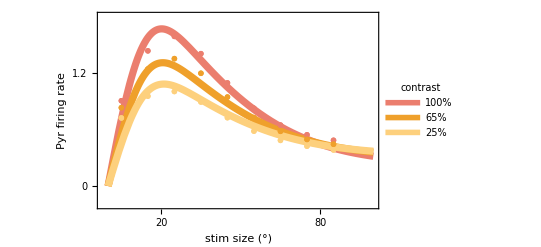

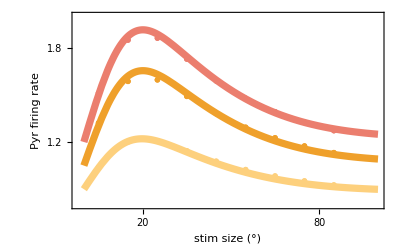

```mathematica
f1=Show[{Plot[Evaluate[Join[{Subscript[rd, fits][s][[aa]]},Table[Subscript[rdcs, fit][s][[c]],{c,1,2}]]],{s,0,100},PlotStyle->ColorData[10]/@{2,3,4},Method->"DefaultPlotStyle"->Thickness[0.013],Evaluate[optionsf1],PlotLegends->Placed[LineLegend[{"100%","65%","25%"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.18,LegendLabel->"contrast"],{0.8,0.6}]],
ListPlot[Table[{{sizs[[i]],stctrl[[i]]}},{i,1,Length[sizs]}],PlotMarkers->{●,20},PlotStyle->colorcontrast[[1]],Evaluate[optionsf1]],ListPlot[Table[{{sizs[[i]],stcontrasts[[i,1]]}},{i,1,Length[sizs]}],PlotStyle->colorcontrast[[2]],PlotMarkers->{●,20},Evaluate[optionsf1]],ListPlot[Table[{{sizs[[i]],stcontrasts[[i,2]]}},{i,1,Length[sizs]}],PlotStyle->colorcontrast[[3]],PlotMarkers->{●,20},Evaluate[optionsf1]]}]
stctrli=Table[LoadFieldCentInv[thismod,s,aa],{s,1,Length[sizs]}];
stcontrastsi=Table[LoadFieldCentInv[c,s,aa],{s,1,Length[sizs]},{c,1004,1005}];
f2=Show[{Plot[Evaluate[Join[{Subscript[ri, fits][s][[aa]]},Table[Subscript[rics, fit][s][[c]],{c,1,2}]]],{s,0,100},PlotStyle->ColorData[10]/@{2,3,4},Method->"DefaultPlotStyle"->Thickness[0.013],Evaluate[optionsf1i]],
ListPlot[Table[{{sizs[[i]],stctrli[[i]]}},{i,1,Length[sizs]}],PlotMarkers->{●,20},PlotStyle->colorcontrast[[1]],Evaluate[optionsf1i]],ListPlot[Table[{{sizs[[i]],stcontrastsi[[i,1]]}},{i,1,Length[sizs]}],PlotStyle->colorcontrast[[2]],PlotMarkers->{●,20},Evaluate[optionsf1i]],ListPlot[Table[{{sizs[[i]],stcontrastsi[[i,2]]}},{i,1,Length[sizs]}],PlotStyle->colorcontrast[[3]],PlotMarkers->{●,20},Evaluate[optionsf1i]]}]
```

## Robustness against errors on σ_AB estimates

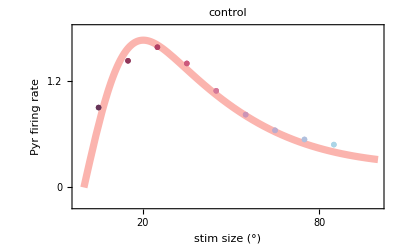

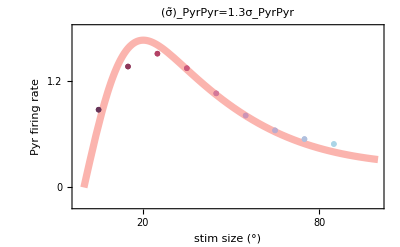

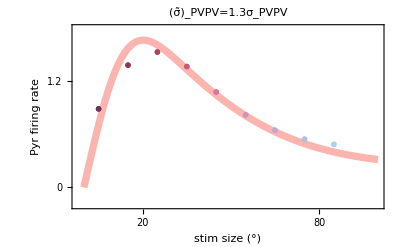

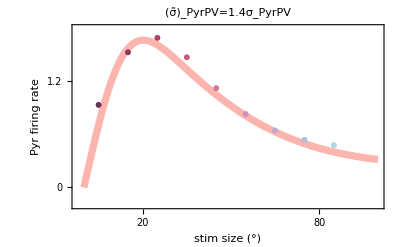

```mathematica
aa=1;
thismod=37;
modsigmaPyrPyr9=1006;
modsigmaPVPV8=1007;
modsigmaPyrPV7=1008;
stctrl=Table[LoadFieldCentDir[thismod,s,aa],{s,1,Length[sizs]}];
stsigmaPyrPyr=Table[LoadFieldCentDir[modsigmaPyrPyr9,s,aa],{s,1,Length[sizs]}];
stsigmaPVPV=Table[LoadFieldCentDir[modsigmaPVPV8,s,aa],{s,1,Length[sizs]}];
stsigmaPyrPV=Table[LoadFieldCentDir[modsigmaPyrPV7,s,aa],{s,1,Length[sizs]}];
(*parfitsmod={{2.6,0.91,16,65},{2.6,0.91,16,65}};
Subscript[rdmodsigmas, fit][s_]:=Table[parfitsmod[[c,1]](Erf[s/parfitsmod[[c,3]]]-parfitsmod[[c,2]]Erf[s/parfitsmod[[c,4]]]),{c,1,2}];*)
f1=Show[{Plot[Subscript[rd, fits][s][[aa]],{s,0,100},Evaluate[optionsf1],PlotLabel->Style["control",30,Darker[Gray]]],ListPlot[Table[{{sizs[[i]],stctrl[[i]]}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]]}]
f2=Show[{Plot[Subscript[rd, fits][s][[aa]],{s,0,100},Evaluate[optionsf1],PlotLabel->Style["(σ̃)_PyrPyr=1.3σ_PyrPyr",30,Darker[Gray]]],ListPlot[Table[{{sizs[[i]],stsigmaPyrPyr[[i]]}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]]}]
f3=Show[{Plot[Subscript[rd, fits][s][[aa]],{s,0,100},Evaluate[optionsf1],PlotLabel->Style["(σ̃)_PVPV=1.3σ_PVPV",30,Darker[Gray]]],ListPlot[Table[{{sizs[[i]],stsigmaPVPV[[i]]}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]]}]
f4=Show[{Plot[Subscript[rd, fits][s][[aa]],{s,0,100},Evaluate[optionsf1],PlotLabel->Style["(σ̃)_PyrPV=1.4σ_PyrPV",30,Darker[Gray]]],ListPlot[Table[{{sizs[[i]],stsigmaPyrPV[[i]]}},{i,1,Length[sizs]}],PlotStyle->ColorData[colorgrads[[aa]]]/@(Range[0,9]/9),PlotMarkers->{●,20},Evaluate[optionsf1]]}]
```

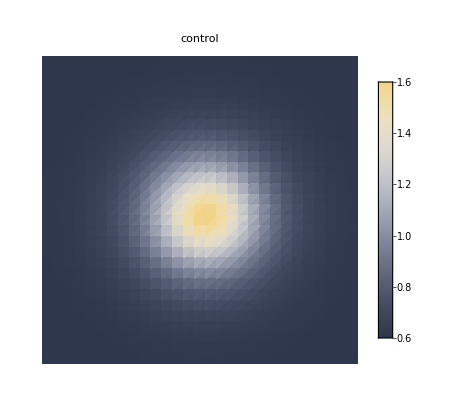

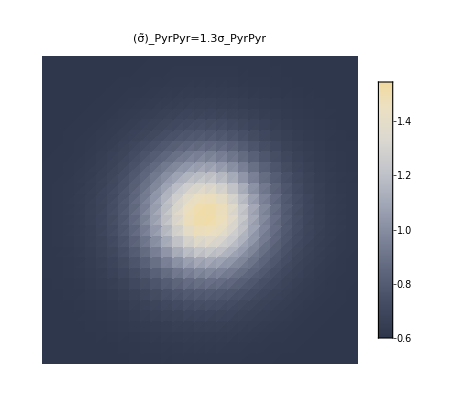

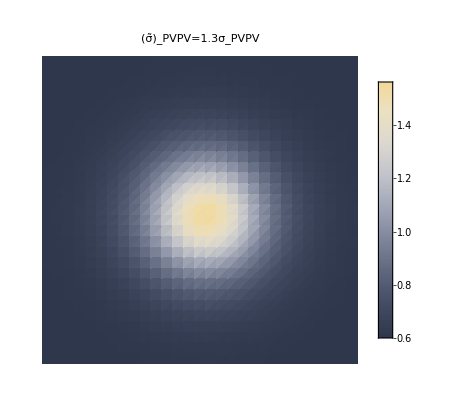

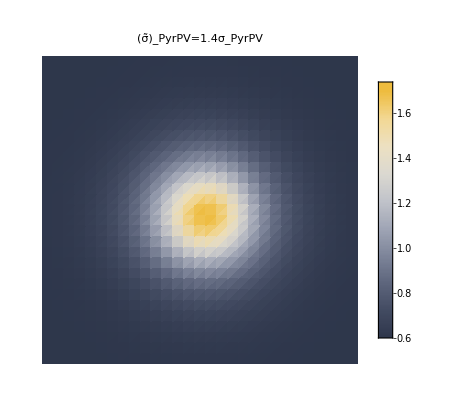

```mathematica
fieldctrl=LoadFieldDir[thismod,3,aa];
fieldsigmaPyrPyr=LoadFieldDir[modsigmaPyrPyr9,3,aa];
fieldsigmaPVPV=LoadFieldDir[modsigmaPVPV8,3,aa];
fieldsigmaPyrPV=LoadFieldDir[modsigmaPyrPV7,3,aa];
f1=ListDensityPlot[fieldctrl,ColorFunction->(ColorData["GrayYellowTones"][Rescale[#1,{0.6,1.7}]]&),PlotRange->All,Frame->False,Mesh->None,PlotLegends->True,ColorFunctionScaling->False,PlotLabel->Style["control",30,Darker[Gray]]]
f2=ListDensityPlot[fieldsigmaPyrPyr,ColorFunction->(ColorData["GrayYellowTones"][Rescale[#1,{0.6,1.7}]]&),PlotRange->All,Frame->False,Mesh->None,PlotLegends->True,ColorFunctionScaling->False,PlotLabel->Style["(σ̃)_PyrPyr=1.3σ_PyrPyr",30,Darker[Gray]]]
f3=ListDensityPlot[fieldsigmaPVPV,ColorFunction->(ColorData["GrayYellowTones"][Rescale[#1,{0.6,1.7}]]&),PlotRange->All,Frame->False,Mesh->None,PlotLegends->True,ColorFunctionScaling->False,PlotLabel->Style["(σ̃)_PVPV=1.3σ_PVPV",30,Darker[Gray]]]
f4=ListDensityPlot[fieldsigmaPyrPV,ColorFunction->(ColorData["GrayYellowTones"][Rescale[#1,{0.6,1.7}]]&),PlotRange->All,Frame->False,Mesh->None,PlotLegends->True,ColorFunctionScaling->False,PlotLabel->Style["(σ̃)_PyrPV=1.4σ_PyrPV",30,Darker[Gray]]]
```

## Inputs to SOM

```mathematica
aa=3;
thread=1009;
inputsSOM=Table[Flatten[Import[StringJoin[parentdir,ToString[thread],"/InputstoSOMcenter_Dirsiz",ToString[sizs[[s]]],"_",ToString[thread],".txt"],"Table"]],{s,1,9}];
```

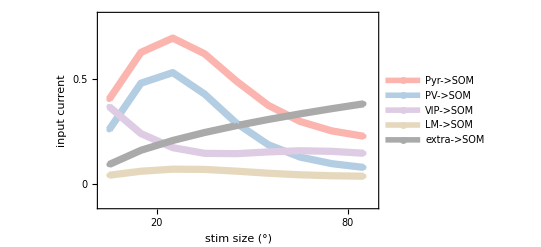

```mathematica
optionsinputs:={PlotRange->{{3,88},{-.1,.8}},Method->"DefaultPlotStyle"->Thickness[0.013],Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotStyle->{colors[[1]],colors[[2]],colors[[4]],colors[[6]],Lighter[Gray]},FrameLabel->{{Style["input current",30,Darker[Gray]],None},{Style["stim size (°)",30,Darker[Gray]],None}},FrameTicks->{{{0,0.5},None},{{20,80},None}},FrameTicksStyle->Directive[30,Darker[Gray]],Joined->True,PlotMarkers->{●,15}};

inputs=ListPlot[Table[{sizs[[s]],Abs[inputsSOM[[s,i]]]},{i,1,5},{s,1,9}],PlotLegends->LineLegend[{"Pyr->SOM","PV->SOM","VIP->SOM","LM->SOM","extra->SOM"},LabelStyle->{GrayLevel[0.3],20},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],Evaluate[optionsinputs]]
```

```mathematica
aa=1;
modsigmaLM5=1010;
modsigmaLM2=1011;
modsigmaLM10=1012;
modsigmaLM15=37;
modsigmaLM20=1013;
modsigmaLM30=1014;
modsigmaLM12=1015;
modsigmaLM25=1016;
modsigmaLM40=1017;
modsigmaLM50=1018;
sLM={2,5,10,12,15,20,25,30,40,50};
fields=Table[LoadFieldInv[thread,2,aa],{thread,{modsigmaLM2,modsigmaLM5,modsigmaLM10,modsigmaLM12,modsigmaLM15,modsigmaLM20,modsigmaLM25,modsigmaLM30,modsigmaLM40,modsigmaLM50}}];
```

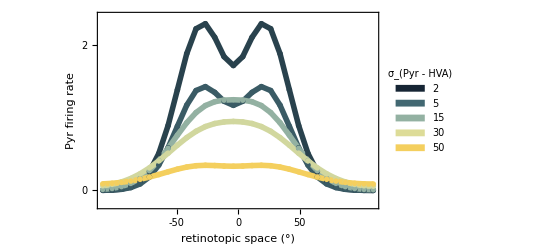

```mathematica
f2=ListPlot[Table[fields[[i,All,center]]-fields[[i,Nn,Nn]],{i,{1,2,5,7,10}}],DataRange->{-110,110},Method->"DefaultPlotStyle"->Thickness[0.01],Joined->True,PlotStyle->ColorData["StarryNightColors"]/@({1,2,5,7,10}/10),PlotRange->{-0.2,2.4},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotMarkers->{●,14},PlotLegends->Placed[SwatchLegend["StarryNightColors",{"2","5","15","30","50"},LabelStyle->{GrayLevel[0.3],Bold,17},LegendLabel->Placed["σ_(Pyr - HVA)",Top],LegendMarkerSize->14],{0.88,0.53}],FrameLabel->{{Style["Pyr firing rate",30,Darker[Gray]],None},{Style["retinotopic space (°)",30,Darker[Gray]],None}},FrameTicks->{{{0,2},None},{{-50,0,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]]]
```

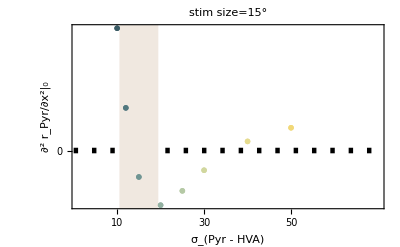

```mathematica
f1=Show[{ListPlot[Table[{{sLM[[i]],fields[[i,center,center]]-fields[[i,center,center+1]]}},{i,3,Length[sLM]}],PlotMarkers->{●,26},PlotStyle->ColorData["StarryNightColors"]/@(Range[2,10]/10),PlotRange->{{1,70},Automatic},Axes->False,Frame->{{True,False},{True,False}},FrameStyle->Thick,PlotLabel->Style["stim size=15°",20,Darker[Gray]],FrameLabel->{{Style["∂^2 r_Pyr/∂x^2|_0",30,Darker[Gray]],None},{Style["σ_(Pyr - HVA)",30,Darker[Gray]],None}},FrameTicks->{{{0},None},{{10,30,50},None}},FrameTicksStyle->Directive[30,Darker[Gray]],GridLines->{{15},None},GridLinesStyle->Directive[LightBrown,Thickness[0.07]]],Plot[0,{sl,0,80},PlotStyle->{Dashing[{0.008,0.025}],Thickness[0.01],Black}]}]
```